```mathematica
data=Import["D:\\Documents\\SocialNetwork\\nn\\NN.txt"];
```

```mathematica
raw=StringSplit[data];
```

```mathematica
a=Table[raw[[3*i+1]],{i,0,2344}];
b=Table[raw[[3*i+2]],{i,0,2344}];
c=Table[raw[[3*i+3]],{i,0,2344}];
```

```mathematica
d=Table[a[[i]]->    b[[i]],{i,1,2345}];
```

```mathematica
e=Table[c[[i]],{i,1,2345}];
```

```mathematica
gg=Graph[d,EdgeWeight->e](*Construct Weighted Graph*)
```

-Graphics-

```mathematica
ggg=Graph[d](*Construct Unweighted Graph*)
```

-Graphics-

```mathematica
CommunityGraphPlot[ggg](*Community Detection for Unweighted Graph*)
```

-Graphics-

```mathematica
sub=FindGraphCommunities[ggg](*Node Classification for Unweighted Graph*)
```

{{1,51,77,2,90,92,158,159,113,69,89,91,17,93,94,121,125,131,4,60,10,16,18,22,24,97,122,126,132,32,7,101,6,102,99,100,27,8,44,37,19,12,41,118,25,30,13,143,28,43,14,144,20,34,40,128,139,140,108,35,107,133,134,36,33,136,161,129,135,120,38,160,130,70,45,141,55,119,137,46,142,114,56,86,138,52,58,85,110,88,49,54,50,96,127,95,166,53,57,63,198,87,84,64,200,199,83,98,124,103,104,115,123,116,214,213,201,202,171},{72,78,71,47,303,73,74,39,174,82,62,193,109,61,75,76,81,48,80,216,154,59,67,178,65,220,66,68,221,111,112,146,225,226,228,229,230,150,234,237,203,217,162,164,253,254,255,204,163,117,177,215,79,148,145,147,192,219,157,172,218,156,170,224,155,173,149,205,206,184,185,194,207,223,208,209,210,211,212},{305,42,189,186,227,235,236,238,239,187,188,240,242,249,250,195,251,252,197,256,276,241,165,169,168,153,196,275,151,277,152,245,278,167,269,272,270,258,274,190,191,244,260,261,262,263,264,265,266,282,279,231,280,232,281,233,246,247,248,243,257,259,267,268,271,273,291,292,293,294,295,296,297,298,299,300},{3,9,21,23,31,5,222,26,11,29,15,105,106,179,180,306,183,175,176,181,182,301,302}}

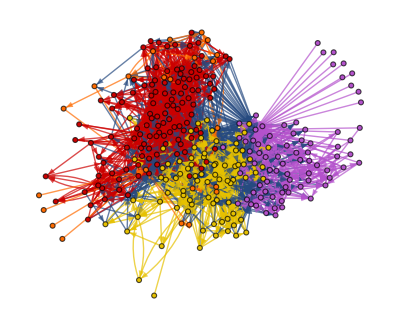

```mathematica
HighlightGraph[ggg,Map[Subgraph[ggg,#]&,%]]
```

```mathematica
BetweennessCentrality[Subgraph[ggg,sub[[1]]]](*Betweeness of the Subgraph*)
```

{22.6546,1114.86,548.688,169.027,1890.39,836.382,304.32,227.087,543.853,6.10162,688.481,233.115,130.497,307.587,244.378,13.7031,2.22991,0.,853.335,90.5329,17.4272,140.928,658.406,118.699,183.965,194.647,11.1763,161.342,0.,7.30138,19.1099,190.662,3.90321,84.6537,620.964,354.048,0.,256.28,244.551,0.,20.5996,0.,568.15,1726.51,150.234,6.96706,2.54627,149.881,24.6733,137.101,449.126,246.574,286.606,21.1331,495.291,893.694,106.204,234.528,98.3072,0.690909,144.226,0.,0.,55.9646,11.0607,128.412,154.122,0.,61.3267,609.087,48.0308,759.384,0.,80.1098,23.4249,64.2642,852.693,291.65,136.185,277.749,196.336,219.259,307.198,16.0395,141.044,490.28,594.065,8.45373,197.05,41.5913,112.346,32.2324,3.98382,1049.26,433.323,518.786,24.6412,0.,170.064,34.1371,409.696,41.7384,146.34,0.,15.8588,582.853,143.159,155.086,80.2488,232.848,103.374,412.97,373.404,138.133,17.8638,13.8746,23.5801,27.085,0.}

```mathematica
BetweennessCentrality[Subgraph[ggg,sub[[2]]]]
```

{209.583,131.328,398.755,170.199,0.,177.588,283.863,6.22897,81.8014,293.607,15.151,57.8269,202.679,27.5061,252.772,275.569,324.129,5.28549,168.593,207.32,66.8095,0.,98.497,338.876,1.57807,195.149,30.3304,61.3214,132.921,175.712,74.3214,2.86244,0.,0.,0.,0.,0.,0.,0.,0.,157.837,359.814,0.,0.,1.68929,1.,0.,61.319,0.,143.781,568.019,106.622,61.0201,119.259,29.4596,111.513,28.6434,152.828,69.1877,14.7365,92.9401,147.984,96.2194,37.4326,1.15087,52.3057,272.836,18.9117,16.0894,4.9094,3.96746,0.,42.4588,32.0005,15.3679,4.53522,0.,0.,0.}

```mathematica
BetweennessCentrality[Subgraph[ggg,sub[[3]]]]
```

{0.,0.,267.333,484.333,53.4167,528.25,130.,189.333,312.167,158.25,18.,0.,0.,68.3333,96.3333,622.417,85.4167,11.25,3.16667,0.,339.167,0.,10.75,53.9167,59.6667,48.5833,455.167,0.,0.,0.,0.,74.1667,0.,272.667,35.75,27.,51.,54.1667,0.,0.,0.,33.8333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.5,0.,0.,19.,153.333,107.333,0.,25.,0.,0.,0.,9.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
BetweennessCentrality[Subgraph[ggg,sub[[4]]]]
```

{0.,0.,5.,0.,1.,12.,24.5,0.,0.,0.,2.,3.,0.,0.5,12.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
vcnt=VertexDegree[ggg]
```

{11,34,80,54,56,15,44,20,22,17,16,12,83,40,26,16,20,11,19,13,19,21,15,21,7,6,7,20,6,11,13,25,13,14,14,18,10,6,9,10,10,15,28,19,134,8,17,25,26,14,17,10,18,12,8,8,8,9,25,37,8,9,13,29,13,12,14,24,9,14,11,25,18,21,21,19,8,17,7,5,2,3,9,10,54,15,54,22,6,12,29,13,5,25,4,20,7,18,34,11,10,17,25,22,11,21,15,13,21,19,11,25,11,22,35,20,15,53,58,35,10,19,19,26,15,59,5,10,5,18,35,13,29,18,8,15,9,52,13,13,7,13,44,5,4,23,5,7,19,19,14,15,11,12,10,13,10,13,9,12,15,14,15,15,11,10,16,14,16,15,14,14,60,12,6,8,12,25,15,14,11,11,12,6,13,16,7,28,8,20,31,34,14,23,11,27,9,17,23,23,18,22,24,21,34,21,15,31,8,16,11,11,10,24,14,12,14,11,22,20,11,10,3,3,18,15,29,11,13,9,8,16,12,19,11,5,7,9,12,10,7,9,1,1,11,23,8,6,6,8,5,2,6,12,6,10,12,11,6,7,1,6,4,5,4,5,4,5,9,12,4,11,5,10,4,14,16,12,8,4,3,2,6,9,16,1,1,1,1,1,1,1,1,1,1,1,1}

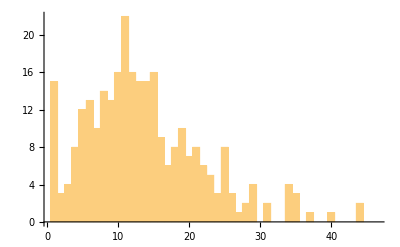

```mathematica
Histogram[vcnt,1000]
```

```mathematica
n1=0
n2=0
n3=0
n4=0
n5=0
n6=0
```

0

0

0

«3 more identical outputs»

```mathematica
For[
j=1,
j≤Length[vcnt],
j++,
{
If[
vcnt[[j]]≥32,
++n6,
{
If[
vcnt[[j]]≥16,
++n5,
{
If[
vcnt[[j]]≥8,
++n4,
{
If[
vcnt[[j]]≥4,
++n3,
{
If[
vcnt[[j]]≥2,
++n2,
{
If[
vcnt[[j]]≥1,
++n1
]
}
]
}
]
}
]
}
]
}
]
}
]
```

```mathematica
n1
```

15

```mathematica
n2
```

7

```mathematica
n3
```

43

```mathematica
n4
```

127

```mathematica
n5
```

82

```mathematica
n6
```

23

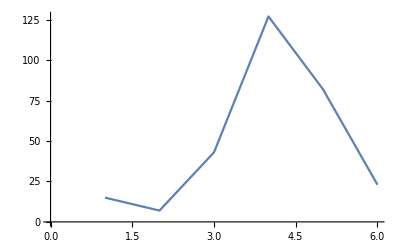

```mathematica
ListPlot[{n1,n2,n3,n4,n5,n6},Joined->True]
```

```mathematica
gg1=Subgraph[ggg,sub[[1]]]
```

-Graphics-

```mathematica
ng1=VertexDegree[gg1]
```

{8,23,24,12,41,19,18,15,15,9,37,21,14,14,16,18,4,4,19,5,9,12,23,12,12,13,15,8,5,8,10,17,6,15,24,24,10,15,15,8,6,8,24,31,6,7,12,20,10,9,13,12,9,13,20,16,19,20,18,7,15,4,3,8,9,12,12,5,9,23,12,18,3,9,8,9,20,17,8,16,11,12,18,8,9,25,16,6,12,12,5,6,5,25,11,22,7,7,14,8,21,11,11,4,12,14,7,15,10,10,9,15,12,15,3,3,5,7,4}

```mathematica
m1=0;m2=0;m3=0;m4=0;m5=0;m6=0;
```

```mathematica
For[
j=1,
j≤Length[ng1],
j++,
{
If[
ng1[[j]]≥32,
++m6,
{
If[
ng1[[j]]≥16,
++m5,
{
If[
ng1[[j]]≥8,
++m4,
{
If[
ng1[[j]]≥4,
++m3,
{
If[
ng1[[j]]≥2,
++m2,
{
If[
ng1[[j]]≥1,
++m1
]
}
]
}
]
}
]
}
]
}
]
}
]
```

```mathematica
m1
```

0

```mathematica
m2
```

4

```mathematica
m3
```

22

```mathematica
m4
```

60

```mathematica
m5
```

31

```mathematica
m6
```

2

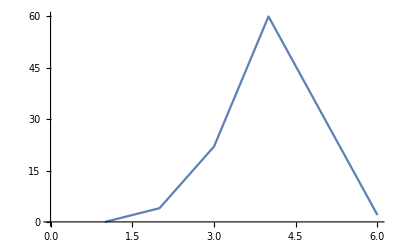

```mathematica
ListPlot[{m1,m2,m3,m4,m5,m6},Joined->True]
```

```mathematica
m1=0;m2=0;m3=0;m4=0;m5=0;m6=0;
```

```mathematica
gg2=Subgraph[ggg,sub[[2]]]
```

-Graphics-

```mathematica
ng2=VertexDegree[gg2]
```

{46,25,45,12,6,36,35,3,13,29,10,15,12,9,41,45,30,10,21,34,10,4,10,26,4,16,5,4,12,18,11,11,6,6,6,8,5,7,9,9,13,37,8,5,6,7,8,12,5,20,24,11,16,18,14,18,15,24,17,9,22,9,8,10,10,11,25,11,8,5,5,4,9,11,10,4,4,1,4}

```mathematica
For[
j=1,
j≤Length[ng2],
j++,
{
If[
ng2[[j]]≥32,
++m6,
{
If[
ng2[[j]]≥16,
++m5,
{
If[
ng2[[j]]≥8,
++m4,
{
If[
ng2[[j]]≥4,
++m3,
{
If[
ng2[[j]]≥2,
++m2,
{
If[
ng2[[j]]≥1,
++m1
]
}
]
}
]
}
]
}
]
}
]
}
]
```

```mathematica
m1
```

1

```mathematica
m2
```

1

```mathematica
m3
```

20

```mathematica
m4
```

33

```mathematica
m5
```

16

```mathematica
m6
```

8

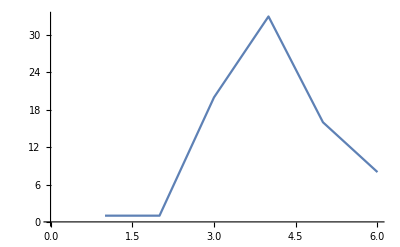

```mathematica
ListPlot[{m1,m2,m3,m4,m5,m6},Joined->True]
```

```mathematica
gg3=Subgraph[ggg,sub[[3]]]
```

-Graphics-

```mathematica
ng3=VertexDegree[gg3]
```

{75,2,16,8,7,8,7,7,7,9,8,7,9,4,7,13,7,6,4,5,12,7,5,11,10,12,7,9,6,10,8,14,8,9,7,5,16,6,7,3,2,8,3,2,3,2,3,2,3,8,10,4,10,5,10,4,12,15,12,8,4,3,2,5,5,13,1,1,1,1,1,1,1,1,1,1}

```mathematica
m1=0;m2=0;m3=0;m4=0;m5=0;m6=0;
```

```mathematica
For[
j=1,
j≤Length[ng3],
j++,
{
If[
ng3[[j]]≥32,
++m6,
{
If[
ng3[[j]]≥16,
++m5,
{
If[
ng3[[j]]≥8,
++m4,
{
If[
ng3[[j]]≥4,
++m3,
{
If[
ng3[[j]]≥2,
++m2,
{
If[
ng3[[j]]≥1,
++m1
]
}
]
}
]
}
]
}
]
}
]
}
]
```

```mathematica
m1
```

10

```mathematica
m2
```

12

```mathematica
m3
```

25

```mathematica
m4
```

26

```mathematica
m5
```

2

```mathematica
m6
```

1

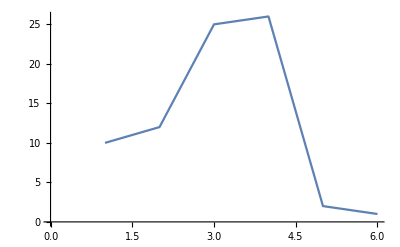

```mathematica
ListPlot[{m1,m2,m3,m4,m5,m6},Joined->True]
```

```mathematica
gg4=Subgraph[ggg,sub[[4]]]
```

-Graphics-

```mathematica
ng4=VertexDegree[gg4]
```

{4,5,6,9,4,5,8,4,4,4,6,2,1,6,6,11,5,1,1,3,3,1,1}

```mathematica
m1=0;m2=0;m3=0;m4=0;m5=0;m6=0;
```

```mathematica
For[
j=1,
j≤Length[ng4],
j++,
{
If[
ng4[[j]]≥32,
++m6,
{
If[
ng4[[j]]≥16,
++m5,
{
If[
ng4[[j]]≥8,
++m4,
{
If[
ng4[[j]]≥4,
++m3,
{
If[
ng4[[j]]≥2,
++m2,
{
If[
ng4[[j]]≥1,
++m1
]
}
]
}
]
}
]
}
]
}
]
}
]
```

```mathematica
m1
```

5

```mathematica
m2
```

3

```mathematica
m3
```

12

```mathematica
m4
```

3

```mathematica
m5
```

0

```mathematica
m6
```

0

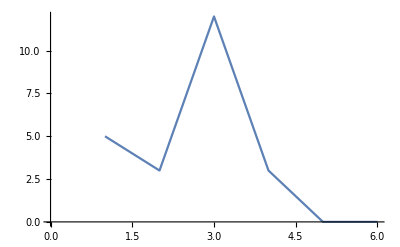

```mathematica
ListPlot[{m1,m2,m3,m4,m5,m6},Joined->True]
```

```mathematica
55
```

```mathematica
G=VertexDegree[d];
```

```mathematica
Length[G]
```

297

```mathematica
Max[b]
```

Max[1,10,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,13,130,131,132,133,134,135,136,137,138,139,14,140,141,142,143,144,145,146,147,148,149,15,150,152,153,154,155,156,157,158,159,16,160,161,162,163,164,165,166,167,168,169,17,170,171,172,173,174,177,178,179,18,180,181,182,183,184,185,186,187,188,189,19,190,192,193,194,195,196,197,198,199,2,20,200,201,202,203,204,205,206,207,208,209,21,213,214,215,216,217,218,219,22,220,221,222,223,224,225,226,227,228,229,23,230,231,232,233,234,235,236,237,238,239,24,240,241,242,244,245,246,247,248,249,25,250,251,252,253,254,255,256,257,258,26,260,261,262,263,264,265,266,268,269,27,270,271,272,274,275,276,277,278,279,28,280,281,282,29,3,30,303,305,306,31,32,33,34,35,36,37,38,39,4,40,41,42,43,44,45,46,47,48,49,5,50,51,52,54,55,56,57,58,59,6,60,61,62,63,65,66,67,68,69,7,70,71,72,73,74,75,76,77,78,79,8,80,81,82,83,84,85,86,87,88,89,9,90,91,92,93,94,95,96,97,98,99]

```mathematica
For[
i=1,
i≤2345,
i++,
{

}
]
```

```mathematica
FindClusters[d]
```

{{51,121,71,72,73,75,76,78,147,82,187,199,205,206,216,217,218,219,192,193,220,221,250,306,188,305},{72,62,73,74,147,79,81,82,178,216,217,193,96,24},{77,144,8,18,20,22,118,99,26,28,32,34,91},{78,305,8,24,101,27,28,305,99},{2,306},{90,93,94,121,126,134},{92,72,25,104,305},{158,77,78,41,4,6,10,14,92,122,99,100,102,27,139,140,107,108,20,71,306,305},{159,78,40,3,9,91,121,122,99,101,26,128,139,140,108,35,180},{113,69,71,77,89,91,158,94,23,189,25,305,54,49,109,51,58,2,91,42,303,109,109,47,146,225,186,226,227,228,229,230,72,73,75,77,150,234,235,236,237,238,239,187,188,240,242,203,179,217,162,164,249,250,195,251,252,253,254,255,197,95,101,99,74,168,169,305,150,168,169,305,227,167,305,189,275,196,305,195,305,276,277,305,282,238,247,279,280,305,228,245,246,276,277,278,279,305,235,276,277,305,257,248,249,281,282,305,305,305},{47,78,9,17,21,93,94,23,121,125,131,31},{60,77,10,16,18,22,93,94,24,97,122,126,132,32,303},{7,222,23,101,305,160},{24,102,305,281},{78,5,121,99,100,101,102,27,305},{77,6,121,122,99,100,101,102,26,44,305,305},{7,23,121,37,305},{8,16,24,122,305,178},{69,5,19,91,23,26,27,29,5},{41,6,94,118,24,25,26,27,30},{143,77,7,19,21,93,118,99,100,27,28,43},{2,9,21,89,118,23,26,27,28,31,178},{10,22,90,118,24,26,27,28,32,44},{122,140,305},{133,89,90,121,100,102,28,127,131,139,108,305},{9,15,93,118,23,102,105,305},{10,16,94,118,24,101,27,106},{19,46,55,56,70,2,40,41,3,4,14,19,20,21,22,89,90,91,92,23,24,27,28,38,303,305,305},{91,146,225,227,228,229,230,72,74,76,78,117,237,178,249,253,256,276,306,127},{92,153,165,305},{305,214},{305,71,72,76,149,203,219},{122,246,256,305},{26,141,52,170,201,67,71,74,77,40,99,100,101,126,131,133,137,43,305,168},{24,102,25,27,36,305},{23,26,27,28,305,96},{73,40,7,94,122,131,136,43},{74,41,8,14,94,99,100,161,129,132,135,44,305},{78,91,122,101,139,140,157,305},{77,78,92,121,102,139,140,169},{74,78,9,89,91,118,120,121,102,133,108,306},{71,77,10,90,92,121,122,101,133,134,107},{77,78,100,303},{78,5,7,17,19,91,93,94,23,120,101,160,126,130,135,29,33,35,116,248},{77,174,6,8,18,20,92,93,94,121,102,161,125,129,136,30,34,36},{69,73,77,82,89,93,158},{70,73,74,78,22,90,94,159,24,100,132,76},{141,55,69,21,89,119,137},{142,114,56,62,70,86,193,90,159,119,135,138,44},{109,51,52,39,58,61,71,72,73,75,76,81,82,85,21,23,139,77,306},{110,52,58,62,72,73,74,75,76,80,82,88,18,216,93,94},{113,189,51,52,115,116,117,187,189,200,190,193,158,159,118,28,123,124,136,305,306},{114,58,306,305},{113,58,71,73,154,92,96,127,128,140,303},{72,74,77,89,91,95,96,127,139,166},{50,57,60,70,1,91,92,303,305},{45,109,51,52,57,63,78,198,89,118,95,135,137,279,305},{110,51,52,77,78,198,90,96,136,138,306,305,305},{46,109,51,52,113,114,87,88,90,219},{49,50,109,110,51,52,113,114,84,87,88},{51,109,170,59,67,74,75,76,78,147,148,79,80,81,220,156,137,303},{54,235,169,276,305},{67,153,178,269,168,305},{110,52},{45,109,51,67,71,73,75,76,89,95,23,119},{142,46,110,52,72,74,75,76,78,178,193,90,161,89,147},{51,113,55,57,58,67,87,88,161},{110,57,62,87,88},{67,220},{68,170,73,74,80,82,192,95,96},{178,55,83,87,88,178,89,91},{221,68,305,177,145,146,226,71,72,73,74,75,76,77,78,117,234,152,240,241,242,244,198,154,203,180,216,222,224,42,134,260,261,262,263,264,265,266},{51,71,72,75,76,207,216,217,195},{111,48,145,73,76,147,79,81,82,192,220,158,119,135,137,168},{65,52,72,17,95,96,123,160},{110,52,112,84},{71,51,72,77,90,118,139,306},{76,225,186,189,274,275,281,282,305},{89,71,198,217,182,306},{114,72,78,90,92,44},{144,146,225,186,226,227,228,229,230,71,74,76,78,150,234,235,236,237,238,239,187,188,240,242,204,180,216,158,162,163,249,250,195,251,252,253,254,255,197,305},{146,225,227,228,229,230,71,73,75,77,117,237,177,249,253,256,276,306,100,247},{146,225,186,228,229,71,73,76,150,234,235,236,237,187,188,241,200,203,215,216,162,163,250,251,252,254,255,305,305},{146,225,186,228,229,72,74,75,150,234,235,236,237,187,188,241,200,204,215,217,162,164,250,251,252,254,255,305},{146,226,227,71,75,150,234,235,236,240,199,216,162,163,165,251,252,253,255,169,276},{146,226,227,72,76,150,234,235,236,240,199,217,162,164,165,251,252,253,255,169,276},{46,74,75,148,80,81,82,86,193,221,96,119,136,138,168},{71,73,74,75,78,148,80,178,216,217,219,221,157,120,164,60},{72,73,74,76,77,147,79,81,172,177,216,217,218,220,163,305},{141,49,113,55,57,59,85},{46,50,114,56,57,58,86,157,119,73},{45,52,55,73,89,136,305},{46,56,60,74,90,119,138,306},{109,110,51,52,113,71,89},{48,110,51,52,113,114,87},{90,97,98,121,122,99,100,101,102,129,139,140,107,108},{4,8,97,121,122,99,100,101,102,128,129,130,131,139,140,107,108,51},{52,69,71,74,76,77,78,89,108,305},{71,72,95,96,98,124,135,139,140,108,137},{142,71,72,136,139,140,107,108,305,247},{71,73,74,91,120,99,100,124,128,103,104,140,107,305,245},{142,51,71,73,74,81,115,92,120,99,100,124,103,104,139,140,305,305},{89,90,99,101,128,132,138,140,305,275},{18,89,90,122,100,123,305,115},{115,142,143,71,72,76,78,82,116,41,154,155,18,158,159,118,100,161,104},{90,144,73,74,82,173,174,150,216,217,222,42,133},{121,248,189,305},{305,144,52,71,72,73,74,75,76,77,78,198,154,216,166,306,280,305},{90,126,104,135,140,107},{122,109,65,67,117,153,199,200,177,160,168,303,281},{305,108,246,305},{121,134,305,82},{71,18,95,96,124,140},{72,52,115,116,100,305},{96,109,55,56,229,61,62,66,67,75,147,81,85,86,237,178,156,95,162,163,255,269,272,305,153,280,305},{139,306},{306},{222,89,90,97,122,140,305},{89,90,98,121,139,305},{141,51,111,55,58,59,67,88,177,156},{142,48,52,56,58,84,88,157,251},{110,147,77,78,115,116,117,40,41,3,4,18,91,92,95,96,121,99,100,139,140,107,108,38},{66,153,245,251,269,169,276,305},{148,305},{177,248,250,305},{46,56,84,177,90,92,238},{73,77,78,172,198,180,183,221,95,96,128,132,306},{198,179,183,192,220,95,96,127,136,139,140,108,306},{146,78,148,234,153,189,193,224,162,164,196,305,127},{55,56,145,69,2,198,177,89,90,43,44},{102,305},{161,147,148,247,199,200,272,305},{100,51,52,72,73,74,77,82,155,95,23,107},{27,160,305},{51,220,247,305},{95,117,153,245,246,247,178,221,194,268,269,271,168,169,276,277,278,279,280,305},{306,71,75,198,178,180,217,245},{306,142,202,62,72,74,75,78,81,119,99,100,101,102,44,305},{71,25,103,305},{28,71,72,75,76,81,207,218,223},{213,28,128,305},{89,306},{90,280,236,278,279,305},{305,189,305},{89,90,305},{73,74,77,81,96,24,98,108},{141,71,72,77,173,40,154,7,13,17,89,156,158,159,118,97,98,99,160,125,130,106,136,33},{71,72,73,74,75,76,81,1,2,198,216,217,192,89,90,43,117},{150,168,305,80,247,277},{73,148,149,80,82,117,177,179,220,166,275,305},{149,72,74,76,78,148,149,81,82,117,173,174,153,245,215,217,218,194,224,157,269,270,196,276,277,305,306},{81,73,74,81,82,116,188,152,240,198,5,6,9,10,180,217,23,24,162,306},{305,237,278,279,305},{146,226,153,168,169,276,277,305},{227,153,245,169,276,277,278,305},{143,144,51,52,71,72,73,74,75,76,198,155},{55,56,201,77,78,115,2,200,91,119,123,126,276},{56,202,78,115,116,2,92,119,125},{153,251,166,168,305},{52,153,95,123,127,128,162,165,251,252,168,169,305},{76,77,173,40,3,216,217,122,160,184},{174,41,4,217,121,129},{143,72,79,82,177,216,218,219,127,29,303},{143,144,171,71,79,81,178,216,217,218,219,128,185,30,195,258},{51,52,55,56,229,61,75,147,81,85,174,237,238,242,177,219,221,157,96,161,162,163,254,255,269,270,272,305,248},{115,198,180,216,183,222,258,306},{116,198,179,217,183,222,258,306},{72,198,216,181,306},{115,172,198,179,216,222,306},{52,170,71,72,77,154,94,120,123},{47,51,71,73,74,198,125,126},{235,187,188,274,275,305},{188,189,275,196,305,305},{187,275,196,305},{141,145,71,72,73,74,76,78,80,117,245,200,217,221,158,306,306},{46,145,71,72,73,74,77,79,117,245,200,216,217,220,90,159,96,306,168},{186,187,188,244,189,203,216,217,250,196,197,305,305},{55,145,69,70,71,73,77,78,152,240,241,242,244,180,216,222,89,90,96,119,128,103,104,135,136,137,138,195,166,260},{51,52,71,72,73,115,116,199,91,158,159,123,124},{103,136,107},{71,72,75,76,82,215,217,222,223},{76,147,149,79,80,187,198,206,207,208,220},{149,80,198,205,207,208,220},{71,72,75,208,216,195},{71,198,203,216,195,246},{80,188,198,204,209,217,195},{128,138},{146,226,71,72,73,74,75,76,77,78,81,117,234,152,240,241,242,244,198,204,179,217,222,223,42,120,133,260,261,262,263,264,265,266},{72,74,76,78,148,149,81,82,117,174,153,245,215,217,219,194,223,157,269,270,196,276,277,305,306},{110,68,148,117,153,199,200,178,157,168,303},{71,75,82,216,194,224,195},{72,76,81,217,194,223,195},{239,274,282,305},{234,169,305},{236,277,278,305},{279,117,245,246,247,248,178,220,272,274,275,196,197,280,281,282,305},{238,280,281,305},{236,245,276,277,305,305},{237,246,277,278,279,305},{239,247,281,282,305},{187,189,274,275,305,245},{229,230,246,247,277,278,279,280,305},{231,232,247,248,278,279,280,281,305},{233,248,189,279,280,281,282,305},{305,189,195,305},{239,274,282,305},{189,195,274,275,305},{153,252,168,169,305},{153,245,253,169,276,305},{245,254,277,305},{246,255,277,278,305},{246,247,305},{178,227,167,305},{147,148,199,200,270,271,305},{305},{305},{305},{305}}

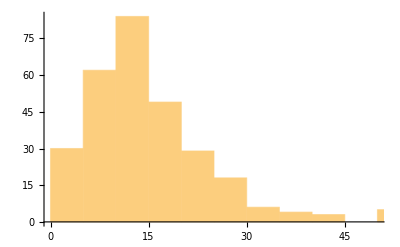

```mathematica
Histogram[G]
```